```mathematica
(* ΔΙΠΛΟ ΟΡΘΟΓΩΝΙΟ ΦΡΕΑΡ ΔΥΝΑΜΙΚΟΥ *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(* ΟΡΙΣΜΟΣ ΣΤΑΘΕΡΩΝ, 1 ΓΙΑ ΑΤΟΜΙΚΑ ΚΑΙ 2 ΓΙΑ ΠΥΡΗΝΙΚΑ ΣΥΣΤΗΜΑΤΑ *)
```

```mathematica
ic=1; 
Which[ ic==1, {c=26.247 , ctime=6.586*10^(-16)},
           ic==2, {c=0.0482, ctime=6.586*10^(-21)}     ];
```

```mathematica
(* ΟΡΙΣΜΟΣ ΠΑΡΑΜΕΤΡΩΝ ΤΟΥ ΔΥΝΑΜΙΚΟΥ *)
```

```mathematica
{v0=300, L0=0.2, v1=200, L1=0.1};
```

```mathematica
(* ΟΡΙΣΜΟΣ ΚΑΙ PLOT ΤΟΥ ΔΥΝΑΜΙΚΟΥ *)
```

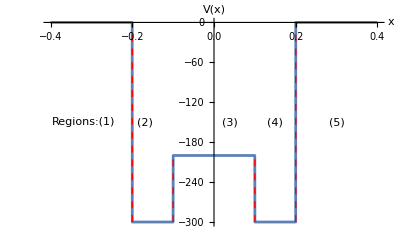

```mathematica
v[x_]:=Which[ L1< Abs[x]≤L0,  -v0 ,
                            Abs[x] >L0, 0 ,
                             Abs[x]<L1, -v1         ]; 
lineStyle={Thick,Red,Dashed};
line1=Line[{{-0.2,-300},{-0.2,0}}];
line2=Line[{{0.2,-300},{0.2,0}}];
line3=Line[{{0.1,-300},{0.1,-200}}];
line4=Line[{{-0.1,-300},{-0.1,-200}}];
 Plot[ v[x], {x, -2*L0, 2*L0}, PlotStyle ->AbsoluteThickness[2],
AxesStyle -> AbsoluteThickness[1], AxesLabel->{"x","V(x)"},
Epilog->{Text[StyleForm["Regions:(1)"], {-0.32, -150}] ,
                  Text[StyleForm[" (2)"], {-0.17, -150}],
                  Text[StyleForm[" (3)"], {0.04, -150}],
                  Text[StyleForm[" (4)"], {0.15, -150}],
                  Text[StyleForm[" (5)"], {0.3, -150}]  ,Directive[lineStyle],line1,line2,line3,line4   }   ]
```

```mathematica
(* ΟΡΙΖΟΥΜΕ ΤΟΥΣ ΚΥΜΑΤΑΡΙΘΜΟΥΣ ΩΣ ΣΥΝΑΡΤΗΣΗ ΤΗΣ ΕΝΕΡΓΕΙΑΣ ΚΑΙ ΤΩΝ ΙΔΙΟΤΙΜΩΝ ΓΙΑ ΤΙΣ ΑΡΤΙΕΣ ΚΑΙ ΤΙΣ ΠΕΡΙΤΤΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
```

```mathematica
(* ΟΡΙΣΜΟΣ ΚΥΜΑΤΑΡΙΘΜΩΝ γ, κ0, κ1 ΩΣ ΣΥΝΑΡΤΗΣΕΙΣ ΤΗΣ ΕΝΕΡΓΕΙΑΣ ΑΠΟ ΤΗΝ ΣΧΕΣΗ 1.80 *)
```

```mathematica
g[e_]:=Sqrt[-c*e]; 
k0[e_]:=Sqrt[c*(e+v0)]; 
k1[e_]:=Sqrt[Abs[c*(e+v1)]];
```

```mathematica
(* ΟΡΙΣΜΟΣ ΕΞΙΣΩΣΕΩΝ ΙΔΙΟΤΙΜΩΝ ΑΡΤΙΩΝ (1.84 & 1.86) ΚΑΙ ΠΕΡΙΤΤΩΝ ΚΑΤΑΣΤΑΣΕΩΝ (1.84 & 1.87) ΩΣ ΣΥΝΑΡΤΗΣΕΙΣ ΤΗΣ ΕΝΕΡΓΕΙΑΣ ΚΑΙ ΤΗΣ ΦΑΣΗΣ *)
```

```mathematica
eqEvenOdd[e_,fi_]:=g[e]*Cos[k0[e]*L0+fi]-k0[e]*Sin[k0[e]*L0+fi];

eq2Even[e_,fi_]:=k0[e]*Sin[k0[e]*L1+fi]*Cosh[k1[e]*L1] + 
                               k1[e]*Cos[k0[e]*L1+fi]*Sinh[k1[e]*L1];  

eq2Odd[e_,fi_]:=k0[e]*Sin[k0[e]*L1+fi]*Sinh[k1[e]*L1] +
                               k1[e]*Cos[k0[e]*L1+fi]*Cosh[k1[e]*L1];
```

```mathematica
(* ΘΑ ΘΕΩΡΗΣΟΥΜΕ ΤΗΝ ΠΕΡΙΠΤΩΣΗ ΟΠΟΥ|E|>V1. Η ΠΕΡΙΠΤΩΣΗ|E|<V1 ΘΑ ΓΙΝΕΙ ΩΣ ΑΣΚΗΣΗ *)
eqEvenOdd[e_,fi_]:=g[e]*Cos[k0[e]*L0+fi]-k0[e]*Sin[k0[e]*L0+fi];
eq1Even[e_,fi_]:=k0[e]*Sin[k0[e]*L1+fi]*Cos[k1[e]*L1] + 
                               k1[e]*Cos[k0[e]*L1+fi]*Sin[k1[e]*L1];  
eq1Odd[e_,fi_]:=k0[e]*Sin[k0[e]*L1+fi]*Sin[k1[e]*L1]+
                                 k1[e]*Cos[k0[e]*L1+fi]*Cos[k1[e]*L1];
```

```mathematica
(* ΕΠΙΛΥΣΗ ΤΟΥ ΣΥΣΤΗΜΑΤΟΣ ΕΞΙΣΩΣΕΩΝ eqEvenOdd[e,fi]=0 ΚΑΙ eq2Even[e,fi]=0 ΓΙΑ ΑΡΤΙΕΣ ΚΑΤΑΣΤΑΣΕΙΣ ΜΕ ΤΗΝ ΕΝΤΟΛΗ FindRoot *)
```

```mathematica
nEven=0;  (* ΑΡΙΘΜΟΣ ΑΡΤΙΩΝ ΚΑΤΑΣΤΑΣΕΩΝ *)
eEven=fiEven=testEven=Table[Null,{20}];
(* Do loop ΜΕΧΡΙ E >-v1 *)
(* ΤΑ ΔΙΑΣΤΗΜΑΤΑ Εmin & Emax ΤΑ ΠΑΙΡΝΟΥΜΕ ΑΠΟ ΤΗΝ ΑΝΤΙΣΤΟΙΧΗ ΣΧΕΣΗ ΓΙΑ ΤΟ ΟΡΘΟΓΩΝΙΟ ΦΡΕΑΡ ΔΥΝΑΜΙΚΟΥ, ΣΧΕΣΗ 1.69 *)
Do[ { Emin=-v0+ (2*n)^2*Pi^2/(4*c*L0^2),
Emax=-v0+ (2*n+1)^2*Pi^2/(4*c*L0^2),
If[Emin >-v1, Break[] ],
If[Emin <-v1, Break[] ],
(* ΕΠΙΛΥΣΗ ΜΕ FindRoot *) 
enfi=FindRoot[{eqEvenOdd[e,fi]==0, eq2Even[e,fi]==0,eq1Even[e,fi]==0},
                         {e,Emin,Emax}, {fi,0,Pi/2}  ],
 (* ΔΥΟ ΡΙΖΕΣ: eSave & fiSave *)
eSave=e/.enfi, fiSave=fi/.enfi,
(* ΕΥΡΕΣΗ ΑΘΡΟΙΣΜΑΤΟΣ ΤΩΝ ΜΕΤΡΩΝ ΤΩΝ eqEvenOdd & eq2Even &eq1Even *)
test=Abs[eqEvenOdd[eSave,fiSave ]] +Abs[eq2Even[eSave,fiSave ]]+Abs[eq1Even[eSave,fiSave]],
Print["e[n=",n,"]=", eSave,"  fi[n=",n,"]=",fiSave," test=",test ],
(* ΕΛΕΓΧΟΣ ΑΚΡΙΒΕΙΑΣ ΤΗΣ ΡΙΖΑΣ *)
(* ΣΕ ΠΕΡΙΠΤΩΣΗ ΠΟΥ ΕΙΝΑ ΟΚ, ΥΠΟΛΟΓΙΖΟΥΜΕ ΤΗΝ ΕΠΟΜΕΝΗ *)
If[test <0.00001,nEven=nEven+1 ;
eEven[[nEven]]=eSave; fiEven[[nEven]]=fiSave;testEven[[nEven]]=test] ,
Clear[Emin, Emax,enfi,eSave, fiSave,test] 
  }, {n,0,10}]
(*  *)
Print["The eingevalues of the even states for |E|>V1 & |E|<V1"]
Do[Print["eEven[",n,"]=",eEven[[n]]," fiEven[",n,"]=",fiEven[[n]]," test=",testEven[[n]] ],
 {n,1,nEven}];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

e[n=0]=-300.736+0.173333 ⅈ  fi[n=0]=1.60606-0.0131308 ⅈ test=1664.3

e[n=1]=-278.326  fi[n=1]=-0.329957 test=2.31992×10^-12

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

e[n=2]=-186.172  fi[n=2]=-0.631176 test=181.456

e[n=3]=-219.061  fi[n=3]=1.23115 test=1.56319×10^-13

The eingevalues of the even states for |E|>V1

eEven[1]=-278.326 fiEven[1]=-0.329957 test=2.31992×10^-12

eEven[2]=-219.061 fiEven[2]=1.23115 test=1.56319×10^-13

```mathematica
(* ΕΥΡΕΣΗ ΜΟΝΑΔΙΚΩΝ ΡΙΖΩΝ *)
```

```mathematica
iev=0;eEven[[nEven+1]]=0.;
(* ΕΛΕΓΧΟΣ ΓΙΑ ΚΑΘΕ ΡΙΖΑ ΠΟΥ ΒΡΗΚΑΜΕ ΑΝ ΕΙΝΑΙ Η ΙΔΙΑ ΜΕ ΤΗΝ ΠΡΟΗΓΟΥΜΕΝΗ *)
Do[{ If[ Abs[eEven[[i]]-eEven[[i+1]] ]<0.0001 ,{ }   ,
 iev=iev+1 ;
eEven[[iev]]=eEven[[i]];fiEven[[iev]]=fiEven[[i]];
Print["Even State Energy[",iev,"]=",eEven[[iev]]] ;
   ]
}, {i,1,nEven+1}]
```

Even State Energy[1]=-278.326

Even State Energy[2]=-219.061

```mathematica
(* ΕΠΙΛΥΣΗ ΤΟΥ ΣΥΣΤΗΜΑΤΟΣ ΕΞΙΣΩΣΕΩΝ eqEvenOdd[e,fi]=0 ΚΑΙ eq2Odd[e,fi]=0 ΓΙΑ ΠΕΡΙΤΤΕΣ ΚΑΤΑΣΤΑΣΕΙΣ ΜΕ ΤΗΝ ΕΝΤΟΛΗ FindRoot *)
```

```mathematica
nOdd=0; (* ΑΡΙΘΜΟΣ ΠΕΡΙΤΤΩΝ ΚΑΤΑΣΤΑΣΕΩΝ *)
eOdd=fiOdd=testOdd=Table[Null,{20}];
(* Do loop ΜΕΧΡΙ E >-v1 *)
(* ΤΑ ΔΙΑΣΤΗΜΑΤΑ Εmin & Emax ΤΑ ΠΑΙΡΝΟΥΜΕ ΑΠΟ ΤΗΝ ΑΝΤΙΣΤΟΙΧΗ ΣΧΕΣΗ ΓΙΑ ΤΟ ΟΡΘΟΓΩΝΙΟ ΦΡΕΑΡ ΔΥΝΑΜΙΚΟΥ, ΣΧΕΣΗ 1.71  *)
Do[ {  Emin=-v0+ (2*n-1)^2*Pi^2/(4*c*L0^2),
Emax=-v0+ (2*n)^2*Pi^2/(4*c*L0^2),
If[Emin >-v1, Break[] ],
(* Do loop ΜΕΧΡΙ E <-v1 *)
If[Emin<-v1,Break[] ],
(* ΕΠΙΛΥΣΗ ΜΕ FindRoot *)
enfi=FindRoot[{eqEvenOdd[e,fi]==0, eq2Odd[e,fi]==0},
                         {e,Emin,Emax}, {fi,0,Pi/2}  ],
enfi1=FindRoot[{eqEvenOdd[e,fi]==0, eq1Odd[e,fi]==0},
                         {e,Emin,Emax}, {fi,0,Pi/2}  ],


(* ΔΥΟ ΡΙΖΕΣ: eSave & fiSave *)
eSave=e/.enfi, fiSave=fi/.enfi,
(* ΕΥΡΕΣΗ ΑΘΡΟΙΣΜΑΤΟΣ ΤΩΝ ΜΕΤΡΩΝ ΤΩΝ eqEvenOdd & eq2Even *)
test=Abs[eqEvenOdd[eSave,fiSave ] ]+ Abs[eq2Odd[eSave,fiSave  ]]+Abs[eq1Odd[eSave,fiSave  ]],
Print["e[",n,"]=", eSave,"  fi[",n,"]=",fiSave," test=",test],
(* ΕΛΕΓΧΟΣ ΑΚΡΙΒΕΙΑΣ ΤΗΣ ΡΙΖΑΣ *)
(* ΣΕ ΠΕΡΙΠΤΩΣΗ ΠΟΥ ΕΙΝΑ ΟΚ, ΥΠΟΛΟΓΙΖΟΥΜΕ ΤΗΝ ΕΠΟΜΕΝΗ *)
If[test <0.00001, nOdd=nOdd+1 ;
eOdd[[nOdd]]=eSave; fiOdd[[nOdd]]=fiSave;testOdd[[nOdd]]=test ],
Clear[Emin,Emax,enfi,eSave, fiSave]
  }, {n,1,10}]
(*  *)
Print["The eingevalues of the odd states for |E|>V1"]
Do[Print["Odd State: e[",n,"]=", eOdd[[n]]," fi[",n,"]=",fiOdd[[n]]," test=",testOdd[[n]] ], {n,1,nOdd}]
```

e[1]=-278.324  fi[1]=-0.330258 test=1.51605×10^-10

e[2]=-278.324  fi[2]=-0.330258 test=3.77298×10^-12

e[3]=-218.654  fi[3]=1.20649 test=1.59162×10^-12

The eingevalues of the odd states for |E|>V1

Odd State: e[1]=-278.324 fi[1]=-0.330258 test=1.51605×10^-10

Odd State: e[2]=-278.324 fi[2]=-0.330258 test=3.77298×10^-12

Odd State: e[3]=-218.654 fi[3]=1.20649 test=1.59162×10^-12

```mathematica
(* ΕΥΡΕΣΗ ΜΟΝΑΔΙΚΩΝ ΡΙΖΩΝ *)
```

```mathematica
iod=0;eOdd[[nOdd+1]]=0;
(* ΕΛΕΓΧΟΣ ΓΙΑ ΚΑΘΕ ΡΙΖΑ ΠΟΥ ΒΡΗΚΑΜΕ ΑΝ ΕΙΝΑΙ Η ΙΔΙΑ ΜΕ ΤΗΝ ΠΡΟΗΓΟΥΜΕΝΗ *)
Do[{ If[ Abs[eOdd[[i]]-eOdd[[i+1]]]<0.0001 ,{ }   ,
iod=iod+1;
eOdd[[iod]]=eOdd[[i]];fiOdd[[iod]]=fiOdd[[i]] ;
Print["Odd State Energy[",iod,"]=",eOdd[[iod]] ];
  ] 
}, {i,1,nOdd+1}];
```

Odd State Energy[1]=-278.324

Odd State Energy[2]=-218.654

The wave function of the even and the odd states

```mathematica
(* ΕΥΡΕΣΗ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΓΙΑ ΑΡΤΙΕΣ ΚΑΙ ΠΕΡΙΤΤΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
```

```mathematica
(* ΟΡΙΣΜΟΣ ΣΤΑΘΕΡΩΝ Α2, Α3, Β3 *)
a2[e_,fi_]:= Exp[-g[e]*L0]/Cos[k0[e]*L0+fi] ;
a3[e_,fi_]:=   a2[e,fi]*Cos[k0[e]*L1+fi]/Cosh[k1[e]*L1];
b3[e_,fi_]:=-a2[e,fi]*Cos[k0[e]*L1+fi]/Sinh[k1[e]*L1];
```

```mathematica
(* ΑΡΤΙΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
```

```mathematica
(* ΟΡΙΣΜΟΣ ΜΗ ΚΑΝΟΝΙΚΟΠΟΙΗΜΕΝΗΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ *)
wf1even[e_,fi_,x_]:= Which[ 
               x≤-L0,  Exp[g[e]*x ]  , 
                x>L0,   Exp[-g[e]*x ],  
   -L0<x≤-L1, a2[e,fi]*Cos[-k0[e]*x+fi] ,
     -L1<x≤L1,  a3[e,fi]*Cosh[k1[e]*x],
        L1<x≤L0, a2[e,fi]*Cos[  k0[e]*x+fi]      ];
(* ΟΡΙΣΜΟΣ ΠΑΡΑΓΟΝΤΑ ΚΑΝΟΝΟΙΚΟΠΟΙΗΣΗΣ *)normeven[e_,fi_]:=Sqrt[2* NIntegrate[wf1even[e,fi,x]^2, {x,-5*L0, 0}
,MaxRecursion->10   ]  ];
(* ΟΡΙΣΜΟΣ ΚΑΝΟΝΙΚΟΠΟΙΗΜΕΝΗΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ *)
wfeven[e_,fi_,x_]:= wf1even[e,fi,x]/normeven[e,fi] ;
```

```mathematica
(* ΓΡΑΦΙΚΟΣ ΥΠΟΛΟΓΙΣΜΟΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΚΑΙ ΠΥΚΝΟΤΗΤΩΝ ΠΙΘΑΝΟΤΗΤΑΣ *)
```

```mathematica
Do[  {   e=eEven[[i]], fi=fiEven[[i]],
figWF=Plot[Evaluate[wfeven[e,fi,x] ], {x, -2*L0, 2*L0}, 
DisplayFunction->Identity,
PlotRange->All, AxesLabel->{"x " ,"  WFeven(x)" }],
figDEN=Plot[Evaluate[wfeven[e,fi,x]^2 ], {x, -2*L0, 2*L0}, 
DisplayFunction-> Identity,
PlotRange->All, AxesLabel->{"x " ,"     DENeven(x)" }],
Print[ " even bound state energy[",i,"]=",eEven[[i]]    ] 
}, {i,1,iev}  ]
```

NIntegrate::inumr: The integrand Which[x≤-0.2,Exp[g[-278.326] x],x>0.2,«5»,0.1<x≤0.2,a2[-278.326,-0.329957] Cos[k0[-278.326] x-0.329957]]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.125,0}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

even bound state energy[1]=-278.326

even bound state energy[2]=-219.061

```mathematica
(* PLOT ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΜΕ ΤΗΝ ΒΟΗΘΕΙΑ ΔΗΜΙΟΥΡΓΙΑΣ ΠΙΝΑΚΑ ΣΤΟΙΧΕΙΩΝ iev ΟΠΟΥ ΕΙΝΑΙ ΤΟ ΠΛΗΘΟΣ ΤΩΝ ΑΡΤΙΩΝ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΠΟΥ ΥΠΟΛΟΓΙΣΤΙΚΑΝ *)
```

```mathematica
figWF=Plot[Evaluate[Table[wfeven[eEven[[i]],fiEven[[i]],x] ,{i,1,iev}]], {x, -0.4, 0.4}, 
 AxesLabel->{"x " ,"  Weven(x)" }]
```

NIntegrate::inumr: The integrand Which[x≤-0.2,Exp[g[-278.326] x],x>0.2,«5»,0.1<x≤0.2,a2[-278.326,-0.329957] Cos[k0[-278.326] x-0.329957]]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.125,0}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

```mathematica
(* PLOT ΠΥΚΝΟΤΗΤΩΝ ΠΙΘΑΝΟΤΗΤΑΣ ΜΕ ΤΗΝ ΒΟΗΘΕΙΑ ΔΗΜΙΟΥΡΓΙΑΣ ΠΙΝΑΚΑ ΣΤΟΙΧΕΙΩΝ iev ΟΠΟΥ ΕΙΝΑΙ ΤΟ ΠΛΗΘΟΣ ΤΩΝ ΑΡΤΙΩΝ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΠΟΥ ΥΠΟΛΟΓΙΣΤΙΚΑΝ *)
```

```mathematica
figDEN=Plot[Evaluate[Table[wfeven[eEven[[i]],fiEven[[i]],x]*wfeven[eEven[[i]],fiEven[[i]],x] ,{i,1,iev}]], {x, -0.4, 0.4}, 
 AxesLabel->{"x " ,"  DENeven(x)" }]
```

NIntegrate::inumr: The integrand Which[x≤-0.2,Exp[g[-278.326] x],x>0.2,«5»,0.1<x≤0.2,a2[-278.326,-0.329957] Cos[k0[-278.326] x-0.329957]]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.125,0}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

```mathematica
(* ΠΕΡΙΤΤΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
```

```mathematica
(* ΟΡΙΣΜΟΣ ΜΗ ΚΑΝΟΝΙΚΟΠΟΙΗΜΕΝΗΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ *)
wf1odd[e_,fi_,x_]:= Which[ 
           x≤-L0,  Exp[g[e]*x ]  ,
             x>L0,  -Exp[-g[e]*x ] ,
 -L0<x≤-L1, a2[e,fi]*Cos[-k0[e]*x+fi] ,
   -L1<x≤L1, b3[e,fi]*Sinh[k1[e]*x],
     L1<x≤L0, -a2[e,fi]*Cos[k0[e]*x+fi]          ];
(* ΟΡΙΣΜΟΣ ΠΑΡΑΓΟΝΤΑ ΚΑΝΟΝΟΙΚΟΠΟΙΗΣΗΣ *)
normodd[e_,fi_]:=Sqrt[2* NIntegrate[wf1odd[e,fi,x]^2, {x,-5*L0, 0}
 ,MaxRecursion->10   ]  ] ;
(* ΟΡΙΣΜΟΣ ΚΑΝΟΝΙΚΟΠΟΙΗΜΕΝΗΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ *)
wfodd[e_,fi_,x_]:= wf1odd[e,fi,x]/normodd[e,fi] ;
```

```mathematica
(* ΓΡΑΦΙΚΟΣ ΥΠΟΛΟΓΙΣΜΟΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΚΑΙ ΠΥΚΝΟΤΗΤΩΝ ΠΙΘΑΝΟΤΗΤΑΣ *)
```

```mathematica
Do[  {  e=eOdd[[i]], fi=fiOdd[[i]],
figWF=Plot[Evaluate[wfodd[e,fi,x] ], {x, -2*L0, 2*L0}, 
DisplayFunction->Identity,
PlotRange->All, AxesLabel->{"x " ,"  WFodd(x)" }],
figDEN=Plot[Evaluate[wfodd[e,fi,x]^2 ], {x, -2*L0, 2*L0}, 
DisplayFunction-> Identity,
PlotRange->All, AxesLabel->{"x " ,"     DENodd(x)" }],
Print[ " odd bound state energy[",i,"]=",eOdd[[i]]   ] 
}, {i,1,iod}  ];
```

NIntegrate::inumr: The integrand Which[x≤-0.2,Exp[g[-278.324] x],«6»,0.1<x≤0.2,-a2[-278.324,-0.330258] Cos[k0[-278.324] x-0.330258]]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.125,0}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

odd bound state energy[1]=-278.324

odd bound state energy[2]=-218.654

```mathematica
(* PLOT ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΜΕ ΤΗΝ ΒΟΗΘΕΙΑ ΔΗΜΙΟΥΡΓΙΑΣ ΠΙΝΑΚΑ ΣΤΟΙΧΕΙΩΝ iod ΟΠΟΥ ΕΙΝΑΙ ΤΟ ΠΛΗΘΟΣ ΤΩΝ ΠΕΡΙΤΤΩΝ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΠΟΥ ΥΠΟΛΟΓΙΣΤΙΚΑΝ *)
```

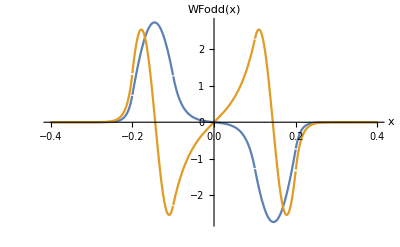

```mathematica
figWF=Plot[Evaluate[Table[wfodd[eOdd[[i]],fiOdd[[i]],x] ,{i,1,iod}]], {x, -0.4, 0.4}, 
 AxesLabel->{"x " ,"  WFodd(x)" }]
```

```mathematica
(* PLOT ΠΥΚΝΟΤΗΤΩΝ ΠΙΘΑΝΟΤΗΤΑΣ ΜΕ ΤΗΝ ΒΟΗΘΕΙΑ ΔΗΜΙΟΥΡΓΙΑΣ ΠΙΝΑΚΑ ΣΤΟΙΧΕΙΩΝ iod ΟΠΟΥ ΕΙΝΑΙ ΤΟ ΠΛΗΘΟΣ ΤΩΝ ΠΕΡΙΤΤΩΝ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΠΟΥ ΥΠΟΛΟΓΙΣΤΙΚΑΝ *)
```

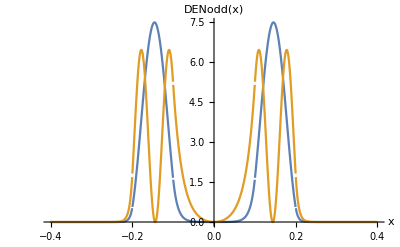

```mathematica
figDEN=Plot[Evaluate[Table[wfodd[eOdd[[i]],fiOdd[[i]],x]^2 ,{i,1,iod}]], {x, -0.4, 0.4}, 
 AxesLabel->{"x " ,"     DENodd(x)" }]
```

```mathematica
(* ΧΡΟΝΙΚΗ ΕΞΕΛΙΞΗ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ ΟΤΑΝ Η ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗ ΕΙΝΑΙ ΤΗΣ ΜΟΡΦΗΣ 1/(√2)(Subscript[u, 0S]+Subscript[u, 1O]) (ΣΧΕΣΗ 1.91) ΚΑΤΑ ΤΗΝ ΧΡΟΝΙΚΗ ΣΤΙΓΜΗ t=0 *)

(* Η ΧΡΟΝΙΚΗ ΕΞΕΛΙΚΗ ΔΙΝΕΤΑΙ ΑΠΟ ΤΗ ΣΧΕΣΗ 
Ψ(x,t)=1/(√2)( Subscript[u, 0S](x) ⅇ^(-Subscript[iE, 0S]t/ℏ)+Subscript[u, 1O](x)ⅇ^(-Subscript[iE, 1O]t/ℏ)) 
Ο ΧΡΟΝΟΣ t ΜΕΤΡΙΕΤΑΙ ΣΕ ΜΟΝΑΔΕΣ ℏ/eV *)
```

```mathematica
DeltaE=eOdd[[1]] - eEven[[1]];
e0S=eEven[[1]]; fi0S=fiEven[[1]];
e1A=  eOdd[[1]]; fi1A=fiOdd[[1]];psi[x_,t_]:=  (wfeven[e0S,fi0S,x] *Exp[-I*e0S*t] + wfodd[e1A,fi1A,x]*Exp[-I*e1A*t] )/Sqrt[2]
tTotal=4*Pi/DeltaE;
tstep=100;
Ntstep=IntegerPart[tTotal/tstep]+1;
Ntstep=10; 
lineStyle={Thick,Red,Dashed};
line5=Line[{{-0.2,0},{-0.2,9}}];
line6=Line[{{0.2,0},{0.2,9}}];
line7=Line[{{0.1,0},{0.1,4}}];
line8=Line[{{-0.1,0},{-0.1,4}}];
vfig[x_]:=Which[ L1< Abs[x]≤L0,  0,Abs[x] >L0,9 , Abs[x]<L1, 4]; 
 TimePlot=Table[
time=tstep*(i-1);
fig=Plot[{vfig[x],Evaluate[ Abs[ psi[x,time] ]  ]}, {x,-1.5*L0,1.5*L0}, PlotRange->All,Epilog->{Directive[lineStyle],line5,line6,line7,line8   }] 
,{i,1,Ntstep}];
```

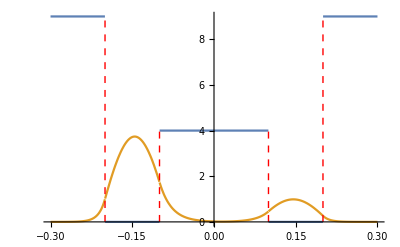

```mathematica
(* PLOT ΓΙΑ ΣΥΓΚΕΚΡΙΜΕΝΗ ΧΡΟΝΙΚΗ ΣΤΙΓΜΗ *)
TimePlot[[3]]
```

```mathematica
(* ΜΕ ΤΗΝ ΕΝΤΟΛΗ ANIMATE ΜΠΡΟΥΜΕ ΝΑ ΔΟΥΜΕ ΟΛΗ ΤΗ ΧΡΟΝΙΚΗ ΕΞΕΛΙΞΗ ΤΗΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ *)
```

```mathematica
Animate[
time=tstep*(i-1);
fig=Plot[{vfig[x],Evaluate[ Abs[ psi[x,time] ]  ]}, {x,-1.5*L0,1.5*L0}, PlotRange->All,Epilog->{Directive[lineStyle],line5,line6,line7,line8   }] 
,{i,1,Ntstep}]
```